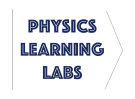
# -Graphics- Lab 1 - Ramp Acceleration

Welcome to your first lab! Today we will be rolling a Pasco smart cart along an inclined plane and recording its acceleration as a function of θ.

This lab consists of a Pasco Smart Cart, a post/base, and a metal ramp inclined at an angle θ.

## Background

### Apparatus

To adjust the angle of inclination:

a) partially unfasten both wingnuts

b) lifting the ramp off the table, use both hands to slide the entire ramp vertically

c) adjust horizontally if needed, and refasten the wingnuts.

** It is important that the ramp does extend past the post. It should be in the same relative horizontal position every trial.

### Capstone

Download the .nb and .cap file. Open the .cap file with Pasco Capstone and turn on your Smart Cart.

Connect the Smart Cart via Bluetooth by entering  and double-clicking on the cart with matching serial numbers. (Make sure only one instance of Capstone is running for successful pairing).

#### General Usage

Ensure cart is oriented as in figure (the flat cart surface should come into contact with the foam, not the velcro).

To start/stop recording sensor data from the Smart Cart, click on .

Each recording is stored as a “run”. If you would like view to specific runs, use the tool

Plot data may be auto-scaled using  . Individual axes can be scaled by moving cursor near the axis number and dragging

## Experiment

### Data Collection

For a given trial, start the cart at the top of the ramp, hit record, and release the cart from rest. Stop recording once the cart reaches the bottom. Scale your data appropriately.

To determine the acceleration, we will be taking the slope of the velocity plot; recall a=dv/dt. 

To calculate the slope, first use the  tool select the relevant data points in the bounding box (only select the points corresponding to motion down the ramp). 

Next use   and select Linear: mx+b. The value of m is the acceleration.

Record the acceleration of the cart for the following six values of θ : {10, 15, 20, 25, 30, 35}. Store your measurements into the variable mydata below in the format: 
{{θ_1, a_1}, {θ_2, a_2}, {θ_3, a_3}, {θ_4, a_4}, {θ_5, a_5}, {θ_6, a_6}}

```mathematica
mydata =
```

### Plotting Experimental Data

To get a feel for your data, use ListPlot to plot mydata. Include appropriate axis labels, i.e. variable and units (for example “a (m/s^2)” ). Add the option PlotStyle→Red and store your plot as variable myplot.

```mathematica
myplot=ListPlot[mydata,PlotStyle->Red,AxesLabel->{"θ (deg.)","a (m/s^2)"},PlotRange->{{0,All},All}]
```

### Linear Fitting

Given our experimental data, we may ask, Can we approximate a(θ) as a linear relationship? If so, what is the equation of the line that describes this relationship?

To determine this, we assume a(θ) to be of the form a=mθ and use the Manipulate function to determine the slope m.

Use the slider to find the slope (m) that minimizes the distance between each data point and the line. This is the line of best fit. You will use the slope m within the analysis section.

```mathematica
Manipulate[Show[myplot, Plot[m θ,{θ,0,35}]],{m,0,1,0.001,Appearance->"Open"}]
```

## Analysis

#### Kinematic Quantities

Pasted images from Capstone should only display the plot region relevant to analysis and must include axes and axes labels.  
To paste images from Capstone, use the Snip and Sketch tool within Windows by clicking on the Start Menu   and typing “sketch”. Once captured,drag the image into the appropriate text cell below and resize.)

For a single trial, paste an image of x(t) from Capstone below.

How does this compare to your prediction from Prelab 1? Contrast any differences.

Now post a screenshot of v(t) below

How does this compare to your prediction from Prelab 1? Contrast any differences.

Post a screenshot of a(t) below

How does this compare to your prediction from Prelab 1? Contrast any differences.

#### a(t) vs. dv/dt

For a single trial, first use  to select the relevant data points within the a(t) plot. Next, use  to find the average acceleration. State the value below.

State the value of a, instead using the slope of the velocity (this is the a within mydata).

How do the two values compare? Which method for determining a(t) is more consistent? Why?

#### a(θ)

Copy and paste an image of the final plot of a(θ ) below ( right-click > copy graphic > paste ). This should include the linear fit and experimental data superimposed.

Using the slope of the fit line, calculate the expected acceleration at 90°. (If you want to do this via code, feel free to create a blank input cell by placing your cursor in-between two cells and typing).

What acceleration do we expect when our ramp is at the physical limit of 90°?

Is the linear fit appropriate for larger values of θ? Why or why not?

Can you think of a (nonlinear) function that might fit our data and also satisfy the physical limit at 90°?

#### Summary

Complete a summary of the lab below. Highlight essential findings and compare experimental results to theoretical model (i.e. the linear fit for this lab).

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).